# Numerical methods for ⅈ u_t+1/2 u_xx+|u|^2 u=0 on a<x<b with periodic BC.

## Method of Lines

We need to define the points at which we are going to approximate solutions.

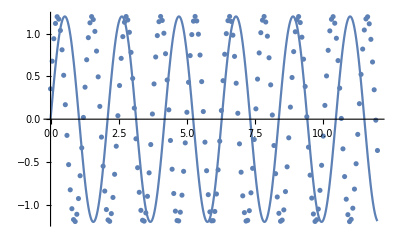

```mathematica
L=12;
{a,b}={0,L};
n=200;
Δx=0.1;
x[j_]:= a+ Δx j
f[x_]:=1.2 Sin[3 x]
fVec=Table[f[x[j]],{j,1,n}];
Show[Plot[f[x],{x,a,b}],
ListPlot[fVec,DataRange->{a,b}]]
```

We need to define and check our approximate differentiation matrices.

We need to understand how to incorporate periodic boundary conditions.

We need to understand (in as many ways as possible) the effects of our different approximate differentiation matrices.

## Spectral Methods

We need to understand and check the Fourier solvers for linear PDEs.  The first thing we need to understand is the order that our FFT puts the pieces in.   We decided we are doing a periodic problem on the interval -L<x<L.  We are going to assume our data is of length n with x_1=-L+Δx, x_2=-L+2 Δx, and x_n=-L+n Δx=L

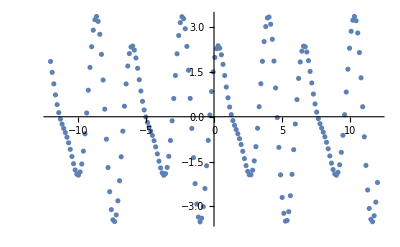

```mathematica
L=12;
n=200;
Δx=2.0L/n;
f[x_]:= 1.2 Cos[3x]+2.4 Sin[2x]+ 0.3 Cos[2x]
x[j_]:=-L+j Δx
fVec=Table[f[x[j]],{j,1,n}];
ListPlot[fVec,DataRange->{-L,L}]
```